# POLINOMIOS DE HERMITE

Queremos Interpolar f(x_k)=P(x_k) y adicionalmente conservar la inclinación f'(x_k)=P'(x_k).

### TEOREMA

#### Si f∈C^1[a,b] y x_0,... ,x_n∈[a,b] son distintos, el único polinomio de menor grado que coincide con f y f’ en x_0,...,x_n es el polinomio de Hermite de grado a lo mas 2n+1, dado por:

#### PH_(2n+1)(x)=∑_(j=0)^n f(x_j)H_j(x)+∑_(j=0)^n f'(x_j)(Ĥ)_j(x)

#### donde

#### H_j(x) = (1 - 2 (x - x_j) L_j^1(x_j))L_j^2(x) (Ĥ)_j(x)=(x-x_j)L_j^2(x)

#### Además, si f∈C^(2n+2)[a,b], entonces:

#### f(x)=PH_(2n+1)(x)+((x-x_0)^2···(x-x_n)^2)/((2n+2)!)f^(2n+2)(ξ(x))

```mathematica
A={{"k","x_k","f(x_k)","f'(x_k)"},{0,1.3,0.6200860,-0.5220232},{1,1.6,0.4554022,-0.5698959},{2,1.9,0.2818186,-0.5811571}}//TableForm
```

k | x_k | f(x_k) | f'(x_k)
0 | 1.3 | 0.620086 | -0.522023
1 | 1.6 | 0.455402 | -0.569896
2 | 1.9 | 0.281819 | -0.581157

Esperamos que el polinomio de Hermite para estos datos sea de grado 5.

#### 1er Paso: Calcular polinomios de Lagrange

```mathematica
f[x_]:= Log[E^(x)+2];
```

```mathematica
Subscript[L, 0][x_]:=((x-(-0.5))(x-0)(x-0.5))/((-1-(-0.5))(-1-0)(-1-0.5))
```

```mathematica
Subscript[L, 1][x_]:=((x-(-1))(x-0)(x-0.5))/((-0.5-(-1))(-0.5-0)(-0.5-0.5))
```

```mathematica
Subscript[L, 2][x_]:=((x-(-1))(x-(-0.5))(x-0.5))/((0-(-0.5))(0-(-1))(0-0.5))
```

```mathematica
Subscript[L, 3][x_]:=((x-(-1))(x-(-0.5))(x-0))/((0.5-(-0.5))(0.5-(-1))(0.5-0))
```

#### 2do Paso: Calcular derivada de Lagrange en los puntos x_k

```mathematica
L0:=N[Subscript[L, 0]'[-1]]
```

```mathematica
L1:=N[Subscript[L, 1]'[-0.5]]
```

```mathematica
L2:=N[Subscript[L, 2]'[0]]
```

```mathematica
L3:=N[Subscript[L, 3]'[0.5]]
```

#### 3er Paso: Calcular los H_k(x)

```mathematica
Subscript[H, 0][x_]:=(1-2(x-(-1))L0)(Subscript[L, 0][x])^2
```

```mathematica
Subscript[H, 1][x_]:=(1-2(x-(-0.5))L1)(Subscript[L, 1][x])^2
```

```mathematica
Subscript[H, 2][x_]:=(1-2(x-0)L2)(Subscript[L, 2][x])^2
```

```mathematica
Subscript[H, 3][x_]:=(1-2(x-0.5)L3)(Subscript[L, 3][x])^2
```

#### 4to Paso: Calcular los (Ĥ)_k(x)

```mathematica
Subscript[Ha, 0][x_]:=(x-(-1))(Subscript[L, 0][x])^2
```

```mathematica
Subscript[Ha, 1][x_]:=(x-(-0.5))(Subscript[L, 1][x])^2
```

```mathematica
Subscript[Ha, 2][x_]:=(x-0)(Subscript[L, 2][x])^2
```

```mathematica
Subscript[Ha, 3][x_]:=(x-0.5)(Subscript[L, 3][x])^2
```

#### 5to Paso: Felicidad

```mathematica
Subscript[PH, 5][x_]:=f[-1]*Subscript[H, 0][x]+f[-0.5]*Subscript[H, 1][x]+f[0]*Subscript[H, 2][x]+f[0.5]*Subscript[H, 3][x]+(0.15536240)*Subscript[Ha, 0][x]+(0.23269654)*Subscript[Ha, 1][x]+(0.33333333)*Subscript[Ha, 2][x]+(0.45186776)*Subscript[Ha, 3][x]
```

```mathematica
Expand[Subscript[PH, 5][x]]
L[x_]:=f[-1]*Subscript[L, 0][x]+f[-0.5]*Subscript[L, 1][x]+f[0]*Subscript[L, 2][x]+f[0.5]*Subscript[L, 3][x]
```

1.09861+0.333333 x+0.111109 x^2+0.0123401 x^3-0.00308241 x^4-0.00100392 x^5+0.0000932136 x^6+0.0000680848 x^7

```mathematica
Expand[L[x]]
```

1.09861+0.332822 x+0.110345 x^2+0.0141405 x^3

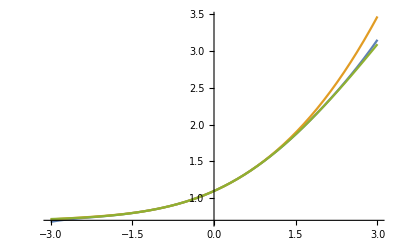

```mathematica
Plot[{Subscript[PH, 5][x],L[x], f[x]},{x,-3,3}]
```

```mathematica
g[x_]:=1.0986122886681098+0.3333333300000004 x+0.11110933596203765 x^2+0.012340130008139383 x^3-0.003082407013323518 x^4-0.0010039177110243713 x^5+0.00009321357129010721 x^6+0.0000680848327441197 x^7;
```

```mathematica
m[x_]:=1.0986122886681098+0.3328215604052218 x+0.1103445600569144 x^2+0.014140484261551123 x^3;
```

```mathematica
g[0.25]
```

1.18907

```mathematica
m[0.25]
```

1.18894

```mathematica
f[0.25]
```

1.18907

```mathematica
Abs[g[0.25]-f[0.25]]
```

1.56043×10^-7